Exercises for Section 24 | More Forms of Visualization

Make a plot with lines joining the squares, the cubes and the 4th powers of integers up to 10. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[{Table[n^2,{n,10}],Table[n^3,{n,10}],Table[n^4,{n,10}]}]
```

-Graphics-

Make a plot of the first 20 primes, joined by a line, filled to the axis and with a red dot at each prime. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[Table[Prime[n],{n,20}],Filling->Axis,Mesh->All,MeshStyle->Red]
```

-Graphics-

Make a 3D plot of the topography for 20 miles around Mount Fuji. |

EXPECTED OUTPUT »

-Graphics- | ×

"ToExpression::sntxi: Incomplete expression; more input is needed .
"

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],5 Quantity[, "Miles"]]]]
```

Cloud::memlimit: This computation has exceeded the memory limit for your plan.

$Aborted

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],20 Quantity[, "Miles"]]]]
```

Cloud::memlimit: This computation has exceeded the memory limit for your plan.

$Aborted

```mathematica
ListPlot3D[QuantityArray[…]]
```

Cloud::memlimit: This computation has exceeded the memory limit for your plan.

$Aborted

```mathematica
"Prgm works, can't run here";
```

Make a relief plot of the topography for 100 miles around Mount Fuji. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ReliefPlot[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],100 Quantity[, "Miles"]]]]
```

-Graphics-

Make a 3D plot of heights generated from Mod[i,j] with i and j going up to 100. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListPlot3D[Table[Mod[i,j],{i,100},{j,100}]]
```

-Graphics3D-

Make a histogram of the differences between successive primes for the first 10000 primes. |

EXPECTED OUTPUT »

-Graphics- | ×

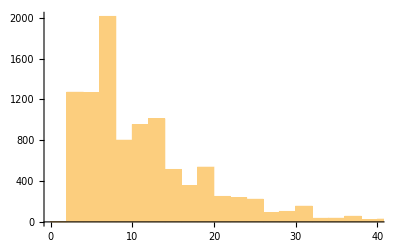

```mathematica
Histogram[Table[Prime[n+1]-Prime[n],{n,10000}]]
```

Make a histogram of the first digits of squares of integers up to 10000 (illustrating Benford’s law). |

EXPECTED OUTPUT »

-Graphics- | ×

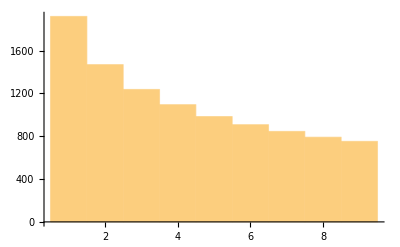

```mathematica
Histogram[Table[IntegerDigits[n^2][[1]],{n,10000}]]
```

Make a histogram of the length of Roman numerals up to 1000. |

EXPECTED OUTPUT »

-Graphics- | ×

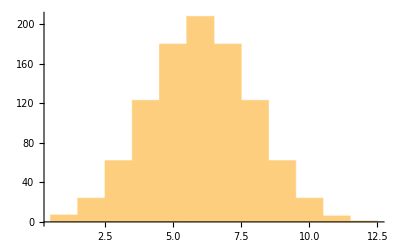

```mathematica
Histogram[Table[StringLength[RomanNumeral[n]],{n,1000}]]
```

Make a histogram of sentence lengths in the Wikipedia article on computers. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

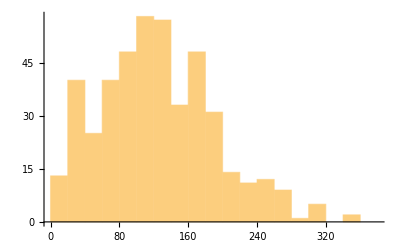

```mathematica
Histogram[StringLength[TextSentences[ WikipediaData["computers"]]]]
```

Make a list of histograms of 10000 instances of totals of n random reals up to 100, with n going from 1 to 5 (illustrating the central limit theorem). |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

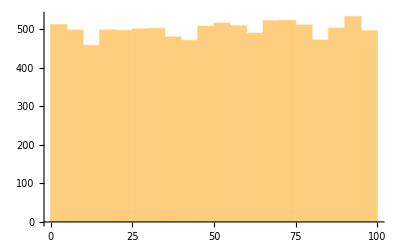
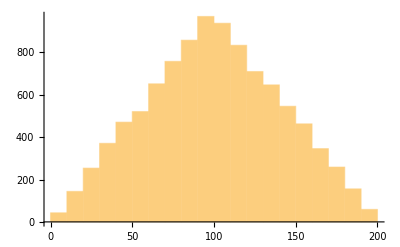
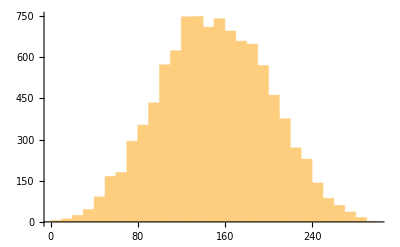
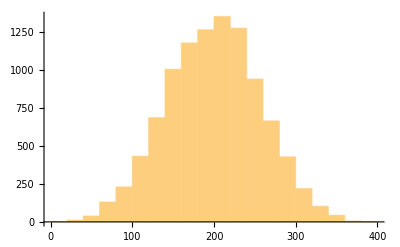
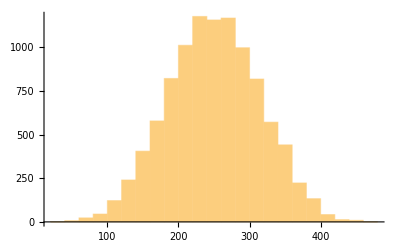

```mathematica
Table[Histogram[Table[Total[RandomReal[{100},n]],10000]],{n,1,5}]
```

Generate a 3D list plot using the image data from a binarized size-200 letter “W” as heights. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListPlot3D[1-ImageData[Binarize[Rasterize[Style["W",200]]]]]
```

-Graphics3D-

```mathematica
ListPlot3D[ImageData[Binarize[Rasterize[Style["W",200]]]]]
```

-Graphics3D-

Make a histogram of word lengths in the Wikipedia article on computers. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

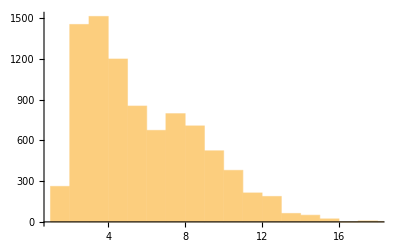

```mathematica
Histogram[StringLength[TextWords[WikipediaData["computers"]]]]
```